```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v2

```mathematica
dataall=Table[Import["./Shi_0-900/Shi_mu="<>ToString[i]<>"_700.0-21x120_VC=true.csv"],{i,0,900,10}];
```

```mathematica
n=Length[Table[i,{i,0,900,10}]]
```

91

```mathematica
dataall[[1]]
```

```mathematica
pdata=Table[Table[Table[dataall[[n1]][[j*120+i]][[5]],{i,2,121}],{j,0,20}],{n1,1,87}];
```

```mathematica
Table[Table[Export["./mub"<>ToString[(i-1)*10+880]<>"/V"<>ToString[j]<>".dat",pdata[[i]][[j]]],{i,1,1}],{j,1,21}];
```

```mathematica
T=Table[i,{i,1,120}];
```

```mathematica
Length[pdata[[1]]]
```

21

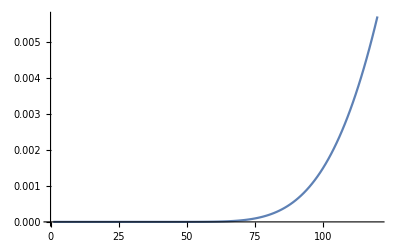

```mathematica
ListLinePlot[pdata[[1]][[10]]*197.33^3/T^4,PlotRange->All]
```